Orders of all finite simple groups, Weyl groups, and Coxeter groups, along with the orders of permutation groups and “classical” matrix groups, related to the four infinite families of simple Lie algebras. Many of these groups are built on algebraic fields, entities that generalize rational numbers.

The order or number of elements of a group is in variable GrpNum with args
- Overall category: “Perm”, “Mat”, “FS”, “CW”
- Abbreviation
- Number (if present)
- Size of algebraic field GF(p^m): power m of prime p (if present)

### What is an algebraic field?

An algebraic field has two operations, conventionally called addition and multiplication. Addition is an abelian group over all the field elements, and multiplication is one also, but over all field elements but the additive identity, 0.The multiplicative identity is 1. The additive inverse of x is -x, and the multiplicative inverse 1/x.

All fields are supersets of either the rational numbers or else of the integers modulo some prime p.

Rational-number supersets: algebraic numbers, computable numbers, definable numbers, real numbers, and complex versions of all of these: complex rational numbers, etc.

Finite fields are all Galois fields, GF(p^m) where p is a prime and m some power of it. GF(p) is the integers modulo p, and GF(p^m) are polynomials in variable x with degree at most m-1, and with coefficients in GF(p). Addition is polynomial addition and multiplication polynomial multiplication modulo a “primitive polynomial”, x^m + some field element, one that cannot be factored in the field. All choices of primitive polynomial give the same field to within isomorphism.

The additive group of GF(p^m) is Z(p)^m, and the multiplicative group Z(p^m-1)

## Permutation Groups

Groups of permutations of symbols.

Sym(n) - symmetric group - group of all permutations with length n
Alt(n) - alternating group  - subgroup of Sym(n0 with all even permutations

Permutation parity: even or odd
Even permutations can be made with an even number of interchanges; odd ones with an odd number.

```mathematica
GrpNum["Perm","Sym",n_] := n!
```

```mathematica
GrpNum["Perm","Alt",n_] := If[n>1,GrpNum["Perm","Sym",n]/2,1]
```

## Classical Matrix Groups

Various groups of matrices over fields

https://www.math.colostate.edu/~hulpke/lectures/m601/ATLASClip.pdf

Prefixes of their name:
G = general ones of some category
S = special ones: determinant = 1
P = projective ones: quotient groups over the the subgroup of all scalar multiples of the identity matrix in that group. Projective ones’ elements are sets of  matrices that are scalar multiples of some matrix, with projective elements’ multiplication being sets made by multiplying their elements.
‘ = commutator or derived subgroup

Linear groups

GL(n,F) - general linear group - all invertible n*n matrices with elements in field F
SL(n,F) - special linear group
PGL(n,F) - projective general linear group
PSL(n,F) or L(n,F) - projective special linear group

For finite fields with order q,
Ordinary Chevalley group A(n,q) = L(n+1,q)

Unitary groups

GU(n,F), SU(n,F), PGL(n,F), and PSU(n,F) -- U(n,F) is either GU(n,F) or PSU(n,F)

Matrix M in GU(n,F) satisfies
M.cjg(tp(M)) = I
where tp is the transpose and cjg is a conjugate operation. For complex numbers, it is the complex conjugate, while for finite fields with even power - GF(q^2) - it is isomorphism x -> x^q

For finite fields with order q^2,
Twisted Chevalley group A2(n,q) = U(n+1,q)
Here, these groups are written with q instead of with q^2, the order of the field, something common.

Symplectic groups

Sp(2n,F) and PSp(2n,F) -- S(2n,F)

Matrix M in Sp(2n,F) satisfies
M.J.tp(M) = J
where tp(J) = - J (antisymmetric) - an example of J is {{0, I}, {-I, 0}}.

In the functions, n is used as the dimension arg instead of 2n.

For finite fields with order q,
Ordinary Chevalley group C(n,q) = S(2n,q)

Orthogonal groups

GO(n,F), SO(n,F), PO(n,F), PSO(n,F), Om(n,F), and PSOm(n,F) -- O(n,F) is either GO(n,F) or POm(n,F)

Matrix M in GO(n,F) satisfies
M.G.tp(M) = G
where tp(G) = G (symmetric)

The orthogonal groups are split by even and odd arg, and the even one is split further:
GO+(2n,F) = GOe+(n,F) and GO-(2n,F) = GOe-(n,F) and GO(2n+1,F)
and likewise for the others.

The Om in Om(n,F) means “Omega”, and Om(n,F) is the commutator subgroup of GO(n,F)

For finite fields with order q,
Ordinary Chevalley group B(n,q) = O(2n+1,q)
Ordinary Chevalley group D(n,q) = O+(2n,q)
Twisted Chevalley group D2(n,q) = O-(2n,q)

Low-order isomorphisms

For finite fields with order q,
SU(2,q) = SL(2,q)
PSU(2,q) = PSL(2,q)
Sp(2,q) = SL(2,q)
PSp(2,q) = PSL(2,q)
POm(3,q) = PSL(2,q)
POm+(4,q) = PSL(2,q)*PSL(2,q)
POm-(4,q) = PSL(2,q^2)
POm(5,q) = PSp(4,q)
POm+(6,q) = PSL(4,q)
POm-(6,q) = PSU(4,q)

GO+-(2,q)
Odd q: 
The dihedral group with order 2(q -+ 1)
Its metric or quadratic form can be taken to be diag({1,-g}) without loss of generality
sqrt(g) is in GF(q) for sign +, GF(q^2) but not in GF(q) for sign -.
SO+-(2,q)
Its cyclic subgroup with order q -+ 1
Even q:
GO+(2,q) only, since every element has a square root.
Taking  g = 1 for convenience,
Elements: a*{{1’s}} +  identity(2)
Multiplying them gives addition in the a’s, group Z2^(power of 2)

PSL(n,q) is simple, except for PSL(2,2) ~ Sym(3) and PSL(2,3) ~ Alt(4)
PSU(n,q) is simple, except for PSU(3,2) = 3^2 : Q8 (order-3^2 abelian group extending order-8 quaternion group)
POm(n,q) is simple for n >= 5, and PSp(2n,q) for n >= 2, except for POm(5,2) = PSp(4,2) ~ Sym(6)

The Chevalley groups, both ordinary (adjoint) and twisted, are related to the simple Lie algebras, both the four classical infinite families and the five exceptional ones.

The parameter n is related to the matrix size, while the parameter q is the order of the field, a prime power.

```mathematica
GrpNum["Mat","GL",n_,q_] := q^(n(n-1)/2)*Product[q^k-1,{k,1,n}]
```

```mathematica
GrpNum["Mat","SL",n_,q_] := q^(n(n-1)/2)*Product[q^k-1,{k,2,n}]
```

```mathematica
GrpNum["Mat","PGL",n_,q_] := GrpNum["Mat","SL",n,q]
```

```mathematica
GrpNum["Mat","PSL",n_,q_] := GrpNum["Mat","SL",n,q]/GCD[n,q-1]
```

```mathematica
GrpNum["Mat","GU",n_,q_] := q^(n(n-1)/2)*Product[q^k-(-1)^k,{k,1,n}]
```

```mathematica
GrpNum["Mat","SU",n_,q_] := q^(n(n-1)/2)*Product[q^k-(-1)^k,{k,2,n}]
```

```mathematica
GrpNum["Mat","PGU",n_,q_] := GrpNum["Mat","SU",n,q]
```

```mathematica
GrpNum["Mat","PSU",n_,q_] := GrpNum["Mat","SU",n,q]/GCD[n,q+1]
```

```mathematica
GrpNum["Mat","Sp",n_,q_] := q^(n^2)*Product[q^(2k)-1,{k,1,n}]
```

```mathematica
GrpNum["Mat","PSp",n_,q_] := GrpNum["Mat","Sp",n,q]/GCD[2,q-1]
```

```mathematica
GrpNum["Mat","GOe+",n_,q_] :=2*q^(n*(n-1))*(q^n-1)*Product[q^(2k)-1,{k,1,n-1}]
```

```mathematica
GrpNum["Mat","GOe-",n_,q_] :=2*q^(n*(n-1))*(q^n+1)*Product[q^(2k)-1,{k,1,n-1}]
```

```mathematica
GrpNum["Mat","GOo",n_,q_] := GCD[2,q-1]*q^(n^2)*Product[q^(2k)-1,{k,1,n}]
```

```mathematica
GrpNum["Mat","SOe+",n_,q_] := GrpNum["Mat","GOe+",n,q]/GCD[2,q-1]
```

```mathematica
GrpNum["Mat","SOe-",n_,q_] := GrpNum["Mat","GOe-",n,q]/GCD[2,q-1]
```

```mathematica
GrpNum["Mat","SOo",n_,q_] := GrpNum["Mat","GOo",n,q]/GCD[2,q-1]
```

```mathematica
GrpNum["Mat","PGOe+",n_,q_] := GrpNum["Mat","SOe+",n,q]
```

```mathematica
GrpNum["Mat","PGOe-",n_,q_] := GrpNum["Mat","SOe-",n,q]
```

```mathematica
GrpNum["Mat","PGOo",n_,q_] := GrpNum["Mat","SOo",n,q]
```

```mathematica
GrpNum["Mat","PSOe+",n_,q_] := GrpNum["Mat","SOe+",n,q]/GCD[2,q-1]
```

```mathematica
GrpNum["Mat","PSOe-",n_,q_] := GrpNum["Mat","SOe-",n,q]/GCD[2,q-1]
```

```mathematica
GrpNum["Mat","PSOo",n_,q_] := GrpNum["Mat","SOo",n,q]
```

```mathematica
GrpNum["Mat","Ome+",n_,q_] :=GrpNum["Mat","SOe+",n,q]/2
```

```mathematica
GrpNum["Mat","Ome-",n_,q_] :=GrpNum["Mat","SOe-",n,q]/2
```

```mathematica
GrpNum["Mat","Omo",n_,q_] := GrpNum["Mat","PSOo",n,q]/GCD[2,q-1]
```

```mathematica
GrpNum["Mat","POme+",n_,q_] :=GrpNum["Mat","GOe+",n,q]/2/GCD[4,q^n-1]
```

```mathematica
GrpNum["Mat","POme-",n_,q_] :=GrpNum["Mat","GOe-",n,q]/2/GCD[4,q^n+1]
```

```mathematica
GrpNum["Mat","POmo",n_,q_] := GrpNum["Mat","Omo",n,q]
```

## Group Matrices

### GO+-(2,q)

Continuous groups O(2) and O(1,1) generalized to finite fields. These are groups over 2*2 matrices of values in field GF(q)

The matrices’ metric has one free quantity, g, and the elements three additional ones: {s,a,b}. They have constraints s^2 = 1 and a^2 - g*b^2 = 1. The determinant of the matrix is s.

With s = 1 only, the group is abelian: cyclic or a product of cyclic groups, like SO(2) and SO(1,1), and with s = +-1, the group is dihedral or a subgroup of  a product of dihedral groups: {all rotations} + {all reflections}, no mixed ones (rotation in one group but reflection in another).

The general case works for real-valued variables and odd-order finite fields, where g is either a square or a non-square value, while for even-order fields, g is always a square and both s values are equivalent. For even-order fields, the group is equivalent to the additive group of the field.

#### General

```mathematica
O2Metric[g_] := DiagonalMatrix[{1,-g}]
```

```mathematica
O2ElemMat[g_,sab_] := Module[{s,a,b},
{s,a,b} = sab;
{{a,b},{g*s*b,s*a}}
]
```

```mathematica
O2Constraint[g_,sab_,x_] := Module[{s,a,b,x1},
{s,a,b} = sab;
x1 = PolynomialRemainder[x,s^2-1,s];
PolynomialRemainder[x1,a^2-g*b^2-1,a]
]
```

```mathematica
O2Constraint[g_,sab_,x_List] := (xi |-> O2Constraint[g,sab,xi]) /@ x
```

```mathematica
O2Mult[g_,sab1_,sab2_] := Module[{s1,a1,b1,s2,a2,b2},
{s1,a1,b1} = sab1;
{s2,a2,b2} = sab2;
{s1*s2,a1*a2 +g*s2*b1*b2, a1*b2 + s2*a2*b1}
]
```

```mathematica
O2Ident[] := {1,1,0}
```

```mathematica
O2Inv[sab_] := Module[{s,a,b},
{s,a,b} = sab;
{s,a,-s*b}
]
```

```mathematica
O2Flip[] := {-1,1,0}
```

```mathematica
O2Tests[] := Module[{g,s1,a1,b1,sab1,elmat1,cstr1,s2,a2,b2,sab2,cstr2,cstr12,elmat2,met,elmtdiff,id,sinv,rot1,rot2,flip,test1,test2,test3,test4},
sab1 = {s1,a1,b1};
elmat1 = O2ElemMat[g,sab1];
cstr1[x_] := O2Constraint[g,sab1,x];
sab2 = {s1,a2,b2};
elmat2 = O2ElemMat[g,sab2];
cstr2[x_] := O2Constraint[g,sab2,x];
cstr12[x_] := cstr2[cstr1[x]];
met = O2Metric[g];
elmtdiff = (el |-> el.met.Transpose[el] - met) @ elmat1;
id = O2Ident[];
sinv = O2Inv[sab1];
rot1 = {1,a1,b1};
rot2 = {1,a2,b2};
flip = O2Flip[];
test1 = cstr1[elmtdiff];
test2 = cstr12[elmat1.elmat2 - O2ElemMat[g,O2Mult[g,sab1,sab2]]];
test3 = cstr1[{Det[elmat1]-s1,O2Mult[g,sab1,id]-sab1,O2Mult[g,id,sab1]-sab1,O2Mult[g,sab1,sinv]-id,O2Mult[g,sinv,sab1]-id}];
test4 = {O2Mult[g,rot1,rot2]-O2Mult[g,rot2,rot1],O2Mult[g,flip,rot1]-O2Mult[g,O2Inv[rot1],flip]};
{test1,test2,test3,test4}
]
```

#### Even field order: characteristic = 2

```mathematica
O2EvenElemMat[a_] := IdentityMatrix[2] + a
```

```mathematica
O2EvenTests[] := Module[{a,b},
Factor[O2EvenElemMat[a].O2EvenElemMat[b]-O2EvenElemMat[a+b],Modulus->2]
]
```

### General Matrix Groups

```mathematica
(* Elements, matrix size *)
```

```mathematica
AllMats[els_,n_] := (blk |-> Partition[blk,n]) /@ Tuples[els,n^2]
```

```mathematica
DetSelMats[els_,reduce_,detsel_,n_] := Select[AllMats[els,n],mat|-> detsel[reduce[Det[mat]]]]
```

```mathematica
(* Scalar: multiple of the identity matrix *)
```

```mathematica
MatIsScalar[mat_] := mat === (mat[[1,1]]*IdentityMatrix[Length[mat]])
```

```mathematica
ScalarMats[mats_] := Select[mats,MatIsScalar]
```

```mathematica
MatScalars[mats_] := #[[1,1]]& /@ ScalarMats[mats]
```

```mathematica
(* Projection-group elements: elements are sets of scalar multiples *)
```

```mathematica
ProjMats[reduce_,mats_] := Module[{scalars},
scalars = MatScalars[mats];
Union[Table[Union[Table[reduce[sc*mat],{sc,scalars}]],{mat,mats}]]
]
```

```mathematica
ProjMatMult[reduce_,pjmat1_,pjmat2_] := Union @@ Table[reduce[mat1.mat2],{mat1,pjmat1},{mat2,pjmat2}]
```

```mathematica
(* Inverses: non-invertible elements and matrices get Null *)
```

```mathematica
ElInvs[els_,reduce_] := If[Length[#]>0,First[#],Null]& /@ Table[Select[els,reduce[el*#]&],{el,els}]
```

```mathematica
MatInvs[els_,reduce_,mats_] := Module[{invs,den,inv},
invs = Thread[els->ElInvs[els,reduce]];
Table[
den = reduce[Det[mat]];
inv = den /. invs;
If[inv=!=Null,reduce[inv*Adjugate[mat]],Null],
{mat,mats}]
]
```

```mathematica
(* Should have some function for using quadratic forms *)
```

```mathematica
?Adjugate
```

### Number-Ring Matrix Groups

```mathematica
(* Matrices *)
```

```mathematica
NREls[np_] := Range[0,np-1]
```

```mathematica
NRReduce[np_,x_] := Mod[x,np]
```

```mathematica
NRMult[np_,mat1_,mat2_] := NRReduce[np,mat1.mat2]
```

```mathematica
AllNRMats[np_,n_] := AllMats[NREls[np],n]
```

```mathematica
GLNRMats[np_,n_] := DetSelMats[NREls[np],NRReduce[np,#]&,GCD[#,np]==1&,n]
```

```mathematica
SLNRMats[np_,n_] := DetSelMats[NREls[np],NRReduce[np,#]&,#==1&,n]
```

```mathematica
NRProjMats[np_,mats_] := ProjMats[NRReduce[np,#1]&,mats]
```

```mathematica
NRMatMult[np_,mat1_,mat2_] := NRReduce[np,mat1.mat2]
```

```mathematica
NRProjMatMult[np_,pjmat1_,pjmat2_] := ProjMatMult[NRReduce[np,#1]&,pjmat1,pjmat2]
```

### Finite Fields

```mathematica
(* Field elements are polynomials modulo p with degree (nmax-1) of some symbol x *)
```

```mathematica
FieldPolys[p_,nmax_,x_] := Module[{coefs,xpwrs},
coefs = NREls[p];
xpwrs =Reverse[NestList[x*#&,1,nmax-1]];
Tuples[coefs,nmax].xpwrs
]
```

```mathematica
FieldPolySeq[p_,nmax_,x_] := Module[{coefs,xpwr=1, plist={0}, pll={}},
coefs = NREls[p];
Do[
plist = Flatten[Outer[Plus,xpwr*coefs,plist,1],1];
AppendTo[pll,plist];
xpwr *= x,
{n,nmax}];
pll
]
```

```mathematica
(* Args: prime number, power of it, symbol *)
```

```mathematica
(* Returns: primitive polynomials with degrees from 1 to x *)
```

```mathematica
FieldPrimPolys[p_,nmax_,x_] := Module[{PrimPolys={},basepolys,xpwr=1,xprlst={},polys,pplys,IsPrim},
If[!PrimeQ[p],Return[]]; If[!IntegerQ[nmax],Return[]]; If[nmax < 1,Return[]];
basepolys = FieldPolySeq[p,nmax,x];
Do[PrependTo[xprlst,xpwr]; xpwr *= x;
polys = xpwr + basepolys[[n]];
pplys = {};
Do[
IsPrim = True;
Do[
Do[
If[PolynomialRemainder[poly,PP,x,Modulus->p]===0,
IsPrim = False; Break[]],
{PP,PPs}];
If[!IsPrim,Break[]],
{PPs,PrimPolys}];
If[!IsPrim,Continue[]];
AppendTo[pplys,poly],
{poly,polys}];
AppendTo[PrimPolys,pplys],
{n,nmax}];
PrimPolys
]
```

```mathematica
(* How many primitive polynomials for power n of prime p *)
```

```mathematica
NumPrimPolys[p_,n_] := (1/n)*DivisorSum[n,d |-> p^d*MoebiusMu[n/d]]
```

```mathematica
(* Test how many *)
```

```mathematica
TestPrimPolyNums[p_,nmax_,x_] := Table[NumPrimPolys[p,n],{n,nmax}] - (Length /@ FieldPrimPolys[p,nmax,x])
```

### Field Matrix Groups

Field data:
Modulus
Variable
Primitive polynomial in that variable

```mathematica
FieldElements[fdata_] := FieldPolys[fdata[[1]],Length[CoefficientList[fdata[[3]],fdata[[2]]]]-1,fdata[[2]]]
```

```mathematica
FieldReduce[fdata_,val_] := PolynomialRemainder[val,fdata[[3]],fdata[[2]],Modulus->fdata[[1]]]
```

```mathematica
FieldReduce[fdata_,vals_List] := Table[FieldReduce[fdata,val],{val,vals}]
```

```mathematica
AllFieldMats[fdata_,n_] := AllMats[FieldElements[fdata],n]
```

```mathematica
GLFieldMats[fdata_,n_] := DetSelMats[FieldElements[fdata],FieldReduce[fdata,#]&,#=!=0&,n]
```

```mathematica
SLFieldMats[fdata_,n_] := DetSelMats[FieldElements[fdata],FieldReduce[fdata,#]&,#===1&,n]
```

```mathematica
FieldProjMats[fdata_,mats_] := ProjMats[FieldMatMult[fdata,#1,#2]&,mats]
```

```mathematica
FieldMatMult[fdata_,mat1_,mat2_] := FieldReduce[fdata,mat1.mat2]
```

```mathematica
FieldProjMatMult[fdata_,pjmat1_,pjmat2_] := ProjMatMult[FieldReduce[fdata,#]&,pjmat1,pjmat2]
```

## Finite Simple Groups

List of finite simple groups - Wikipedia
https://en.wikipedia.org/wiki/List_of_finite_simple_groups

These are groups with no normal subgroups, no subgroups with separate conjugate subgroups.

Alternating groups

Alt(n)

Groups of Lie type (Chevalley groups, Steinberg groups, ...)

As matrix groups:
A(n,q) = PSL(n+1,q)
A2(n,q) = PSU(n+1,q)
B(n,q) = POm(2n+1,q)
C(n,q) = PSp(2n,q)
D(n,q) = POm+(2n,q)
D2(n,q) = POm-(2n,q)

Isomorphisms:
A(1,q) = A2(1,q) = B(1,q) = C(1,q)
D(2,q) = A(1,q) * A(1,q)
B(2,q) = C(2,q)
D(3,q) = A(3,q)
B(n,2^m) = C(n,2^m)

Simple:
A(1,4) = A(1,5) = Alt(5)-- 60
A(1,7) = A(2,2) -- 168
A(1,9) = Alt(6) -- 360
A(3,2) = Alt(8) -- 20160
A2(3,2) = B(2,3) -- 25920

Solvable:
D(1,q) -- (q-1)/gcd(4,q-1)
A(1,2) = Sym{3) -- 6
A(1,3) = Alt(4) -- 12
A2(2,2) -- (order-3^2 abelian group extending order-8 quaternion group) -- 72
B2(2,2) -- (Frobenius group: Z4 acting on Z5) -- 20

With a simple commutator subgroup:
B(2,2) = Sym(6) -- 720
Index 2: B’(2,2) = A(1,9) = Alt(6) -- 360
F2(4,2) -- index 2: F2’(4,2) -- 17971200
G(2,2) -- index 2: G’(2,2)  = A2(2,3) -- 6048
G2(2,3) -- index 3: G2’(2,3) = A(1,8) -- 504

The only sets of non-isomorphic finite simple groups with the same size:
B(n,q) and C(n,q) for n >= 3 and q odd
A(2,4) and A(3,2) = Alt(8) -- 20160

```mathematica
GrpNum["FS","A",n_,q_] := GrpNum["Mat","PSL",n+1,q]
```

```mathematica
GrpNum["FS","A2",n_,q_] := GrpNum["Mat","PSU",n+1,q]
```

```mathematica
GrpNum["FS","B",n_,q_] := GrpNum["Mat","POmo",n,q]
```

```mathematica
GrpNum["FS","B'",2,2] := GrpNum["FS","B",2,2]/2
```

```mathematica
GrpNum["FS","C",n_,q_] := GrpNum["Mat","PSp",n,q]
```

```mathematica
GrpNum["FS","D",n_,q_] := GrpNum["Mat","POme+",n,q]
```

```mathematica
GrpNum["FS","D2",n_,q_] := GrpNum["Mat","POme-",n,q]
```

```mathematica
GrpNum["FS","D3",4,q_] := q^12*(q^8+q^4+1)*(q^6-1)*(q^2-1)
```

```mathematica
GrpNum["FS","E",6,q_] := q^36/GCD[3,q-1]*Product[q^k-1,{k,{2,5,6,8,9,12}}]
```

```mathematica
GrpNum["FS","E",6,q_] := q^36/GCD[3,q+1]*Product[q^k-(-1)^k,{k,{2,5,6,8,9,12}}]
```

```mathematica
GrpNum["FS","E",7,q_] := q^63/GCD[2,q-1]*Product[q^k-1,{k,{2,6,8,10,12,14,18}}]
```

```mathematica
GrpNum["FS","E",6,q_] := q^120*Product[q^k-1,{k,{2,8,12,14,18,20,24,30}}]
```

```mathematica
GrpNum["FS","F",4,q_] := q^24*Product[q^k-1,{k,{2,6,8,12}}]
```

```mathematica
GrpNum["FS","G",2,q_] := q^6*Product[q^k-1,{k,{2,6}}]
```

```mathematica
GrpNum["FS","G'",2,2] := GrpNum["FS","G",2,2]/2
```

```mathematica
GrpNum["FS","B2",2,pwr_] := (q |-> q^2*(q^2+1)*(q-1)) @ (2^(2*pwr+1))
```

```mathematica
GrpNum["FS","F2",4,pwr_] := (q |-> q^12*(q^6+1)*(q^4-1)*(q^3+1)*(q-1)) @ (2^(2*pwr+1))
```

```mathematica
GrpNum["FS","F2'",4,0] := GrpNum["FS","F2",4,0]/2
```

```mathematica
GrpNum["FS","G2",2,pwr_] := (q |-> q^3*(q^3+1)*(q-1)) @ (3^(2*pwr+1))
```

```mathematica
(* Sporadic groups *)
```

```mathematica
(* Mathieu *)
```

```mathematica
GrpNum["FS","M",11] = 7920;
```

```mathematica
GrpNum["FS","M",12] = 95040;
```

```mathematica
GrpNum["FS","M",22] = 443520;
```

```mathematica
GrpNum["FS","M",23] = 10200960;
```

```mathematica
GrpNum["FS","M",24] = 244823040;
```

```mathematica
(* Janko *)
```

```mathematica
GrpNum["FS","J",1] = 175560;
```

```mathematica
GrpNum["FS","J",2] = 604800;
```

```mathematica
GrpNum["FS","J",3] = 50232960;
```

```mathematica
GrpNum["FS","J",4] = 86775571046077562880;
```

```mathematica
(* Conway *)
```

```mathematica
GrpNum["FS","Co",1] = 4157776806543360000;
```

```mathematica
GrpNum["FS","Co",2] = 42305421312000;
```

```mathematica
GrpNum["FS","Co",3] = 495766656000;
```

```mathematica
(* Fischer *)
```

```mathematica
GrpNum["FS","Fi",22] = 64561751654400;
```

```mathematica
GrpNum["FS","Fi",23] = 4089470473293004800;
```

```mathematica
GrpNum["FS","Fi'",24] = 1255205709190661721292800;
```

```mathematica
(* Higman-Sims *)
```

```mathematica
GrpNum["FS","HS"] = 44352000;
```

```mathematica
(* McLaughlin *)
```

```mathematica
GrpNum["FS","McL"] = 898128000;
```

```mathematica
(* Held *)
```

```mathematica
GrpNum["FS","He"] = 4030387200;
```

```mathematica
(* Rudvalis *)
```

```mathematica
GrpNum["FS","Ru"] = 145926144000;
```

```mathematica
(* Suzuki *)
```

```mathematica
GrpNum["FS","Suz"] = 448345497600;
```

```mathematica
(* O'Nan *)
```

```mathematica
GrpNum["FS","O'N"] = 460815505920;
```

```mathematica
(* Harada-Norton *)
```

```mathematica
GrpNum["FS","HN"] = 273030912000000;
```

```mathematica
(* Lyons *)
```

```mathematica
GrpNum["FS","Ly"] = 51765179004000000;
```

```mathematica
(* Thompson *)
```

```mathematica
GrpNum["FS","Th"] = 90745943887872000;
```

```mathematica
(* Baby Monster *)
```

```mathematica
GrpNum["FS","B"] = 4154781481226426191177580544000000;
```

```mathematica
(* Fischer-Griess Monster *)
```

```mathematica
GrpNum["FS","M"] = 808017424794512875886459904961710757005754368000000000;
```

### History of Sporadic Groups

```mathematica
SporGrpDscv = {{1861,{"M",11},{"M",12}},{1873,{"M",22},{"M",23},{"M",24}},{1966,{"J",1}},{1968,{"HS"},{"Co",1},{"Co",2},{"Co",3}},{1969,{"Suz"},{"J",2},{"J",3},{"McL"},{"He"}},{1971,{"Fi",22},{"Fi",23},{"Fi'",24}},{1972,{"Ly"}},{1973,{"Ru"},{"B"},{"M"},{"Th"},{"HN"}},{1976,{"O'N"},{"J",4}}};
```

```mathematica
(* How many sporadic groups are accounted for? Should be 26 *)
```

```mathematica
Flatten[Rest /@ SporGrpDscv,1] // Length
```

26

```mathematica
TableForm[SporGrpDscv]
```

1861 | M
11 | M
12 |  |  | 
1873 | M
22 | M
23 | M
24 |  | 
1966 | J
1 |  |  |  | 
1968 | HS | Co
1 | Co
2 | Co
3 | 
1969 | Suz | J
2 | J
3 | McL | He
1971 | Fi
22 | Fi
23 | Fi'
24 |  | 
1972 | Ly |  |  |  | 
1973 | Ru | B | M | Th | HN
1976 | O'N | J
4 |  |  |

```mathematica
(* Added the order of the first simple group discovered: Alt(5) *)
```

```mathematica
SporGrpDscvOrds = {{1832,{{"Alt",5},60}}} ~Join~ ((yent |-> Join[{First[yent]},(gent |-> {gent,GrpNum @@ Join[{"FS"},gent]}) /@ Rest[yent]]) /@ SporGrpDscv)
```

{{1832,{{Alt,5},60}},{1861,{{M,11},7920},{{M,12},95040}},{1873,{{M,22},443520},{{M,23},10200960},{{M,24},244823040}},{1966,{{J,1},175560}},{1968,{{HS},44352000},{{Co,1},4157776806543360000},{{Co,2},42305421312000},{{Co,3},495766656000}},{1969,{{Suz},448345497600},{{J,2},604800},{{J,3},50232960},{{McL},898128000},{{He},4030387200}},{1971,{{Fi,22},64561751654400},{{Fi,23},4089470473293004800},{{Fi',24},1255205709190661721292800}},{1972,{{Ly},51765179004000000}},{1973,{{Ru},145926144000},{{B},4154781481226426191177580544000000},{{M},808017424794512875886459904961710757005754368000000000},{{Th},90745943887872000},{{HN},273030912000000}},{1976,{{O'N},460815505920},{{J,4},86775571046077562880}}}

```mathematica
(* Galois discovering simplicity of Alt(5) added *)
```

```mathematica
MakeStr[xlst_] := StringJoin @@ (ToString /@ xlst)
```

```mathematica
SporOrdsYrs = Flatten[(yent |-> Labeled[{First[yent],#[[2]]},MakeStr[#[[1]]]]& /@ Rest[yent]) /@ SporGrpDscvOrds,1];
```

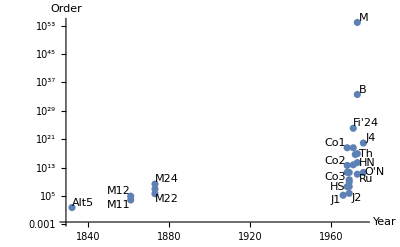

```mathematica
ListLogPlot[SporOrdsYrs,AxesLabel->{"Year","Order"}]
```

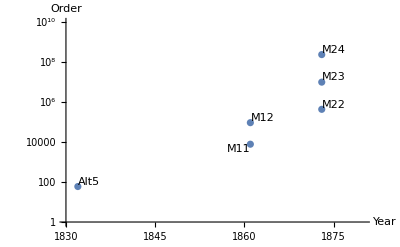

```mathematica
ListLogPlot[SporOrdsYrs,PlotRange->{{1830,1880},{1,10^10}},AxesLabel->{"Year","Order"}]
```

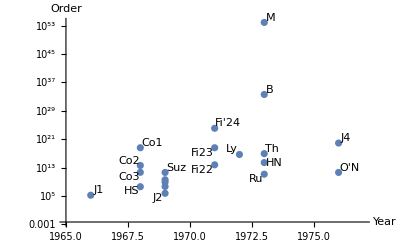

```mathematica
ListLogPlot[SporOrdsYrs,PlotRange->{{1965,1977},Automatic},AxesLabel->{"Year","Order"}]
```

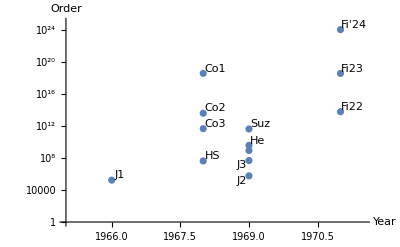

```mathematica
ListLogPlot[SporOrdsYrs,PlotRange->{{1965,1971+1/2},{1,10^25}},AxesLabel->{"Year","Order"}]
```

## Coxeter and Weyl Groups

Coxeter group - Wikipedia
https://en.wikipedia.org/wiki/Coxeter_group

Weyl group - Wikipedia
https://en.wikipedia.org/wiki/Weyl_group

Coxeter groups have generators r(i) interrelated with (r(i)*r(j))^(m(i.j)) = e
where symmetric matrix m has  m(i,i) = 1 and m(i,j), j != i, is a positive integer greater than 1, or infinity (oo).

Weyl groups are a subset of Coxeter groups, with m’s restricted to 2, 3, 4, and 6 - the crystallographic set

All generators are involutions. A pair of generators with m = 2 commutes.
Schläfli matrix: - 2 * cos(pi/m)

Coxeter diagram: each node is for a generator, and each edge has the m value for the generators that it connects.. Edges with m = 2 are omitted, and edges without numbers are assumed to have m = 3.

Dynkin diagrams are related, but with only m = 2, 3, 4, and 6 allowed. They correspond to 0, 1, 2, and 3 lines between two nodes.

All these Coxeter groups are also Weyl groups for simple Lie algebras:
A(n) : string of n nodes -- Sym(n)
-- n = 1: flip group Z2
-- n = 2: dihedral group Dih(3)
B(n), C(n): string of n nodes, with the last edge having (4)
-- hyperoctahedral group: signed permutation matrices: each nonzero element is +-1
-- n = 2: dihedral group Dih(4)
-- n = 3: octahedral group Oh
D(n): string of n-1 nodes, with a one-node branch at node n-
 -- like the above, with an even number of minus signs.
 -- n = 2: dihedral group DIh(2) -- flip group
 -- n = 3: pyritohedral group Td
 E6: string of 5 nodes, with a 1-node branch from the 3rd one
 E7: like the above, with 6 nodes
 E8: like the above, with 7 nodes
 F4: string of 4 nodes, with the middle edge having (4)
 -- hyperdiamond symmetry group: signed permutations + invertible matrices with all elements +-1/2
 G2: string of 2 nodes, with the edge having (6)
 -- dihedral group Dih(6)
 
 No simple Lie algebras correspond to these Coxeter groups:
 H(n): string of n nodes, with the first edge having (5)
 -- n = 2: dihedral group Dih(5)
 -- n = 3:  icosahedral group Ih -- icosahedral rotation group I * inversion
 -- n = 4: hypericosahedral group
 -- no higher values of n
 I(m): string of 2 nodes, with the edge having (m)
 -- dihedral group Dih(m)
 I(m) overlaps with all the others with 2 generators: m = 2, 3, 4, 5, 6
 Different from the others: m >= 7
 
Proofs:
Classification of Finite Coxeter Groups
by Shourya Mukherjee
https://math.uchicago.edu/~may/REU2019/REUPapers/Mukherjee.pdf
The Classification of Simple Complex Lie Algebras
by Joshua Bosshardt
https://math.uchicago.edu/~may/REU2012/REUPapers/Bosshardt.pdf

```mathematica
GrpNum["CW","A",n_] := GrpNum["Perm","Sym",n+1]
```

```mathematica
GrpNum["CW","B",n_] := 2^n*GrpNum["Perm","Sym",n]
```

```mathematica
GrpNum["CW","C",n_] := GrpNum["CW","B",n]
```

```mathematica
GrpNum["CW","D",n_] := (1/2)*GrpNum["CW","B",n]
```

```mathematica
GrpNum["CW","E",6] := 51840
```

```mathematica
GrpNum["CW","E",7] := 2903040
```

```mathematica
GrpNum["CW","E",8] := 696729600
```

```mathematica
GrpNum["CW","F",4] := 1152
```

```mathematica
GrpNum["CW","G",2] := 12
```

```mathematica
GrpNum["CW","H",2] := 10
```

```mathematica
GrpNum["CW","H",3] := 120
```

```mathematica
GrpNum["CW","H",4] := 14400
```

```mathematica
GrpNum["CW","I",n_] := 2n
```

```mathematica
TestCW[] := {GrpNum["CW","B",1] - GrpNum["CW","A",1],Table[GrpNum["CW",type,2],{type,Characters["DABHG"]}]- Table[GrpNum["CW","I",n],{n,{2,3,4,5,6}}],{GrpNum["Mat","GOe-",1,2],GrpNum["Mat","GOe+",1,4]}-GrpNum["CW","I",3],{GrpNum["Mat","GOe-",1,3],GrpNum["Mat","GOe+",1,5]}-GrpNum["CW","I",4],{GrpNum["Mat","GOe-",3,2],GrpNum["Mat","SOo",2,3],2*GrpNum["Mat","PSp",2,3],2*GrpNum["Mat","PSU",4,2]}-GrpNum["CW","E",6],{2*GrpNum["Mat","GOo",3,2],2*GrpNum["Mat","Sp",3,2]}-GrpNum["CW","E",7],{2*GrpNum["Mat","GOe+",4,2]}-GrpNum["CW","E",8],{GrpNum["Mat","GOe+",2,3]}-GrpNum["CW","F",4]}
```

```mathematica
TestCW[]
```

{0,{0,0,0,0,0},{0,0},{0,0},{0,0,0,0},{0,0},{0},{0}}

### Coxeter-Weyl matrices